```mathematica
hullcurve = 2*Abs[x/2]^3
hull = (x≥-2&&x≤2&&y≥0&&y≤10&&z≥hullcurve&&z≤2)
hullreg = ImplicitRegion[True,{{x,-2,2},{y, 0, 10}, {z, hullcurve, 2}}]
hulldensity = 300
waterdensity = 1000
ballastdensity = 5000000/(81*π)
ballast = ImplicitRegion[x^2+(z-0.09)^2≤0.09^2&&y≥0&&y≤10, {x,y,z}]
boatdens = Piecewise[{{ballastdensity+hulldensity, {x,y,z}∈ballast}}, hulldensity]
Show[RegionPlot3D[hullreg,PlotStyle->Directive[Yellow,Opacity[0.5]],Mesh->None], RegionPlot3D[ballast, PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None]]
```

Abs[x]^3/4

x≥-2&&x≤2&&y≥0&&y≤10&&z≥Abs[x]^3/4&&z≤2

ImplicitRegion[-2≤x≤2&&0≤y≤10&&Abs[x]^3/4≤z≤2,{x,y,z}]

300

1000

5000000/(81 π)

ImplicitRegion[x^2+(-0.09+z)^2≤0.0081&&y≥0&&y≤10,{x,y,z}]

Piecewise[{{300+5000000/(81 π), {x,y,z}∈ImplicitRegion[x^2+(-0.09+z)^2≤0.0081&&y≥0&&y≤10,{x,y,z}]}, {300, True}}]

-Graphics3D-

```mathematica
Waterline[θ_]:= ImplicitRegion[z≤Tan[θ*π/180]*x+draft,{{x,-2,2}, {y,0,10}, {z,0,2}}]
Mass[boatregion_, boatdensity_]:=Integrate[boatdensity,{x, y, z}∈boatregion]
CenterOfMass[boatregion_, boatdensity_]:= 1/Mass[boatregion, boatdensity]*Integrate[boatdensity * {x,y,z}, {x,y,z}∈boatregion]
CalculateDraft[boatregion_, boatdensity_, θ_]:=NSolve[Integrate[1, {x,y,z}∈RegionIntersection[boatregion, Waterline[θ]]]==Mass[boatregion, boatdensity]/1000, draft][[1]]
DisplacedWater[boatregion_, boatdensity_, θ_]:= RegionIntersection[boatregion, Waterline[θ]]/.CalculateDraft[boatregion, boatdensity, θ]
CenterOfBuoyancy[boatregion_, boatdensity_, θ_]:=1000/Mass[boatregion, boatdensity] * Integrate[{x,y,z}, {x,y,z}∈DisplacedWater[boatregion, boatdensity, θ]]
RightingMoment[boatregion_, boatdensity_, θ_]:=Cross[CenterOfBuoyancy[boatregion, boatdensity, θ]-CenterOfMass[boatregion, boatdensity], Mass[boatregion, boatdensity]*9.8*{-Sin[θ*π/180], 0, Cos[θ*π/180]}]
```

RightingMoment successfully calculates the vector torque exerted by the water on a boat with a hull shape defined by a given region, density as a given function of {x,y,z}, and a given heel angle in degrees. Units are in kg and m, to convert to cm and g replace any instance of the number 1000 with the number 1.

```mathematica
RightingMoment[hullreg, boatdens,175]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{5.98301×10^-10,-15235.2,-5.23445×10^-11}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{5.98301×10^-10,-15235.2,-5.23445×10^-11}

While this is all fine and dandy, if we’re going to be looking at 3D boats, we might as well look at how it’s going to right itself in 3D, meaning taking into consideration longitudinal tip as well as heel

```mathematica
Waterline3D[θ_, ϕ_]:= Quiet[ImplicitRegion[Piecewise[{{y, ϕ==90},{x, θ==90},{-z, θ>90||ϕ>90}},z]≤Piecewise[{{draft, θ==90||ϕ==90},{-1*(Tan[θ*π/180]*x+Tan[ϕ*π/180]*y+draft), θ>90||ϕ>90}},Tan[θ*π/180]*x+Tan[ϕ*π/180]*y+draft],{{x,-2,2}, {y,0,10}, {z,0,2}}]]
CalculateDraft3D[boatregion_, boatdensity_, θ_, ϕ_]:=Quiet[NSolve[Integrate[1, {x,y,z}∈RegionIntersection[boatregion, Waterline3D[θ, ϕ]]]==Mass[boatregion, boatdensity]/1000, draft][[1]]]
DisplacedWater3D[boatregion_, boatdensity_, θ_, ϕ_]:= Quiet[RegionIntersection[boatregion, Waterline3D[θ, ϕ]]/.CalculateDraft3D[boatregion, boatdensity, θ, ϕ]]
CenterOfBuoyancy3D[boatregion_, boatdensity_, θ_, ϕ_]:=Quiet[1000/Mass[boatregion, boatdensity] * Integrate[{x,y,z}, {x,y,z}∈DisplacedWater3D[boatregion, boatdensity, θ, ϕ]]]
RightingMoment3D[boatregion_, boatdensity_, θ_, ϕ_]:=Quiet[Cross[CenterOfBuoyancy3D[boatregion, boatdensity, θ, ϕ]-CenterOfMass[boatregion, boatdensity], Mass[boatregion, boatdensity]*9.8*{-Tan[θ*π/180], -Tan[ϕ*π/180],1}/Piecewise[{{-1, θ>90||ϕ>90}},1]/Norm[{-Tan[θ*π/180], -Tan[ϕ*π/180],1}]]]
```

```mathematica
RightingMoment3D[hullreg, boatdens,89, 0]
CalculateDraft3D[hullreg, boatdens,89, 0]
CenterOfBuoyancy3D[hullreg, boatdens,89, 0]
Integrate[1, {x,y,z}∈DisplacedWater3D[hullreg, boatdens, 89, 0]]
RegionPlot3D[DisplacedWater3D[hullreg, boatdens, 89, 0]]
```

{-1.04817×10^-11,-64060.3,-6.00495×10^-10}

{draft→-19.0735}

{0.990145,5.,1.18094}

23.

-Graphics3D-

```mathematica
f[angle_]:=N[Norm[RightingMoment3D[hullreg, boatdens,angle, 0]]*Piecewise[{{-1, RightingMoment3D[hullreg, boatdens,angle, 0][[2]]>0}},1]]
angleTable=Quiet[Parallelize[Table[{angle,f[angle]},{angle,1,179,2}]]]
```

{{1,3039.19},{3,9125.42},{5,15235.2},{7,21384.6},{9,27589.9},{11,33867.9},{13,40236.},{15,46712.6},{17,53316.8},{19,60068.8},{21,66990.1},{23,74103.5},{25,81433.5},{27,89005.9},{29,96848.7},{31,104906.},{33,111999.},{35,117873.},{37,122671.},{39,126510.},{41,129484.},{43,131676.},{45,133155.},{47,133982.},{49,134209.},{51,133886.},{53,133053.},{55,131752.},{57,130016.},{59,127879.},{61,125372.},{63,122521.},{65,119353.},{67,115892.},{69,112160.},{71,108179.},{73,103969.},{75,99548.5},{77,94934.8},{79,90144.3},{81,85192.6},{83,80094.3},{85,74863.7},{87,69514.6},{89,64060.3},{91,58514.1},{93,52888.7},{95,47197.},{97,41451.6},{99,35665.},{101,29850.},{103,24018.9},{105,18184.5},{107,12359.6},{109,6557.13},{111,790.236},{113,-4927.6},{115,-10582.5},{117,-16160.3},{119,-21646.},{121,-27024.},{123,-32278.2},{125,-37391.},{127,-42344.},{129,-47117.1},{131,-51688.6},{133,-56034.5},{135,-60128.4},{137,-63940.6},{139,-67437.3},{141,-70580.},{143,-73323.9},{145,-75616.3},{147,-77394.5},{149,-78582.4},{151,-79087.},{153,-78791.8},{155,-77548.4},{157,-75164.5},{159,-71384.2},{161,-65858.3},{163,-58428.2},{165,-50907.2},{167,-43636.9},{169,-36578.5},{171,-29695.5},{173,-22953.3},{175,-16319.1},{177,-9761.21},{179,-3248.71}}

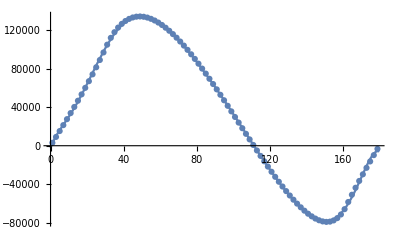

{134799.,{x→49.5344}}

111.36

```mathematica
bestFit=Fit[angleTable,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
Plot[bestFit,{x,0,180}];
ListPlot[angleTable];
Show[%,%%]
root=FindRoot[bestFit,{x,90}];
maxTorque=FindMaximum[bestFit,{x,45}]
avs=root[[1,2]]
```